## Introduction

Try and find fixed points “by hand” when  E > 0

### Ideas

1. Sub trig to polynomial: x=sin θ, cosθ=±√(1-x^2) etc
2. Search for solutions with x1=x2, θ1=θ2 etc

## Attempt 1

### ODEs

```mathematica
Clear[b,j,k]
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Find fp

#### Move from trig --> polynomail

Here I’m only including one branch of fixed points. So I’m searching for *a* fixed point -- not *all* fixed points.

```mathematica
sub={
Cos[xp]->x,
Sin[xp]->√(1-x^2),
Cos[xm]->y,
Sin[xm]->√(1-y^2),
Cos[θp]->w,
Sin[θp]->√(1-w^2),
Cos[θm]->z,
Sin[θm]->√(1-z^2)
};

TableForm[es]
es1=TrigExpand[es]/.sub;
TableForm[es1]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

e-x √(1-y^2)
-√(1-x^2) y-k y √(1-y^2) z^2+k y √(1-y^2) (1-z^2)
e-w √(1-z^2)
-√(1-w^2) z-k y^2 z √(1-z^2)+k (1-y^2) z √(1-z^2)

Looking at these, I can do the elimination one by om

### Solve one by one

#### First FP

```mathematica
xsol=Solve[es1[[1]]==0,x][[1,1]]
```

x→e/(√(1-y^2))

```mathematica
zsol=(Solve[(es1[[2]]/.xsol)==0,z]//Simplify)[[1,1]]
```

z→-(ⅈ √(-k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))/(√2 √k (1-y^2)^(1/4))

```mathematica
wsol=Solve[es1[[3]]==0,w][[1,1]]
```

w→e/(√(1-z^2))

```mathematica
temp=es1[[4]]/.xsol/.zsol/.wsol/.zsol//Simplify
```

(ⅈ √(-k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))) (√2 √(((1-2 e^2) k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))+k (-1+2 y^2) √(1+(√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)))))/(2 √k (1-y^2)^(1/4))

Need to clean this up

```mathematica
temp1=Numerator[temp]
```

ⅈ √(-k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))) (√2 √(((1-2 e^2) k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))+k (-1+2 y^2) √(1+(√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2))))

Now I set both factors equal to zero and find the fp

```mathematica
temp2=temp1[[2]]
```

√(-k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))

```mathematica
ysol1=FullSimplify[Solve[temp2==0,y],{e>0}]
```

{{y→-(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)},{y→(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)},{y→-(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)},{y→(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)}}

Ok, so here are some fixed points. Now the second term

```mathematica
$Assumptions={e>0};
```

```mathematica
xsol/.ysol1
```

{x→e/(√(1+(1-2 k^2+√(1-4 e^2 k^2))/(2 k^2))),x→e/(√(1+(1-2 k^2+√(1-4 e^2 k^2))/(2 k^2))),x→e/(√(1-(-1+2 k^2+√(1-4 e^2 k^2))/(2 k^2))),x→e/(√(1-(-1+2 k^2+√(1-4 e^2 k^2))/(2 k^2)))}

```mathematica
zsol/.ysol//Simplify
```

{z→-(ⅈ √(-√2 k √((1+√(1-4 e^2 k^2))/k^2)+2 √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1+√(1-4 e^2 k^2))/k^2)^(1/4)),z→-(ⅈ √(-√2 k √((1+√(1-4 e^2 k^2))/k^2)+2 √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1+√(1-4 e^2 k^2))/k^2)^(1/4)),z→-(ⅈ √(-k √((2-2 √(1-4 e^2 k^2))/k^2)+2 √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1-√(1-4 e^2 k^2))/k^2)^(1/4)),z→-(ⅈ √(-k √((2-2 √(1-4 e^2 k^2))/k^2)+2 √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1-√(1-4 e^2 k^2))/k^2)^(1/4))}

```mathematica
wsol/.zsol/.ysol//Simplify
```

{w→e/(√((1+√(1-4 e^2 k^2)+√2 k √((1+√(1-4 e^2 k^2))/k^2) √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2))))/(2+2 √(1-4 e^2 k^2)))),w→e/(√((1+√(1-4 e^2 k^2)+√2 k √((1+√(1-4 e^2 k^2))/k^2) √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2))))/(2+2 √(1-4 e^2 k^2)))),w→(√2 e)/(√((-1+√(1-4 e^2 k^2)-k √((2-2 √(1-4 e^2 k^2))/k^2) √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2))))/(-1+√(1-4 e^2 k^2)))),w→(√2 e)/(√((-1+√(1-4 e^2 k^2)-k √((2-2 √(1-4 e^2 k^2))/k^2) √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2))))/(-1+√(1-4 e^2 k^2))))}

```mathematica
ysol1//Flatten
```

{y→-(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2),y→(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2),y→-(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2),y→(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)}

```mathematica
fp1={xsol/.ysol1,ysol1//Flatten,zsol/.ysol,wsol/.zsol/.ysol}ᵀ//Simplify;
TableForm[fp1]
```

x→(√2 e)/(√((1+√(1-4 e^2 k^2))/k^2)) | y→-(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2) | z→-(ⅈ √(-√2 k √((1+√(1-4 e^2 k^2))/k^2)+2 √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1+√(1-4 e^2 k^2))/k^2)^(1/4)) | w→e/(√((1+√(1-4 e^2 k^2)+√2 k √((1+√(1-4 e^2 k^2))/k^2) √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2))))/(2+2 √(1-4 e^2 k^2))))
x→(√2 e)/(√((1+√(1-4 e^2 k^2))/k^2)) | y→(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2) | z→-(ⅈ √(-√2 k √((1+√(1-4 e^2 k^2))/k^2)+2 √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1+√(1-4 e^2 k^2))/k^2)^(1/4)) | w→e/(√((1+√(1-4 e^2 k^2)+√2 k √((1+√(1-4 e^2 k^2))/k^2) √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2))))/(2+2 √(1-4 e^2 k^2))))
x→(√2 e)/(√((1-√(1-4 e^2 k^2))/k^2)) | y→-(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2) | z→-(ⅈ √(-k √((2-2 √(1-4 e^2 k^2))/k^2)+2 √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1-√(1-4 e^2 k^2))/k^2)^(1/4)) | w→(√2 e)/(√((-1+√(1-4 e^2 k^2)-k √((2-2 √(1-4 e^2 k^2))/k^2) √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2))))/(-1+√(1-4 e^2 k^2))))
x→(√2 e)/(√((1-√(1-4 e^2 k^2))/k^2)) | y→(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2) | z→-(ⅈ √(-k √((2-2 √(1-4 e^2 k^2))/k^2)+2 √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1-√(1-4 e^2 k^2))/k^2)^(1/4)) | w→(√2 e)/(√((-1+√(1-4 e^2 k^2)-k √((2-2 √(1-4 e^2 k^2))/k^2) √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2))))/(-1+√(1-4 e^2 k^2))))

Hmm, I was expecting some symmetry. But recall, this is just for one set of fixed points (and not *all*) fixed points.

```mathematica
subC={C[1]->0,C[2]->0,C[3]->0,C[4]->0};
Manipulate[
p1=ListPlot[{x,y}/.fp1/.subC/.k->k1/.e->e1,
PlotStyle->PointSize[Large],
AxesLabel->{"x1","x2"},
LabelStyle->15,
AxesOrigin->{0,0},
PlotRange->{{-π,π},{-π,π}},
ImageSize->Medium
];

p2=ListPlot[{w,z}/.fp1/.subC/.k->k1/.e->e1,
PlotStyle->PointSize[Large],
AxesLabel->{"θ1","θ2"},
LabelStyle->15,
AxesOrigin->{0,0},
PlotRange->{{-π,π},{-π,π}},
ImageSize->Medium
];

Grid[{{p1,p2}}]
,
{{k1,0.01},-5,5},{e1,0.01,1}
]
```

#### Rest of FP

```mathematica
temp3=temp1[[3]]
```

√2 √(((1-2 e^2) k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))+k (-1+2 y^2) √(1+(√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)))

Ok, this one is hard. Let me plot it first

```mathematica
Manipulate[Plot[temp3/.{k->k1,e->e1},{y,-3,3},AxesOrigin->{0,0}],{k1,-3,3},{e1,0,3}]
```

Hmm... so there are two real solution, it seems.

```mathematica
Solve[temp3==0,y]
```

$Aborted

I’ll have to try and clean it first by hand

```mathematica
Simplify[Together[temp3]]
```

√2 √(((1-2 e^2) k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))+k (-1+2 y^2) √(1+(√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)))

Can I turn this into  a polynomial in y?

```mathematica
ysol2=FullSimplify[Solve[temp1[[3]]==0,y],{e>0}]
```

$Aborted

## Attempt 2

### ODEs

```mathematica
Clear[b,j,k]
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Find fp

#### Move from trig --> polynomail

Here I’m only including one branch of fixed points. So I’m searching for *a* fixed point -- not *all* fixed points.

```mathematica
sub={
Cos[xp]->x,
Sin[xp]->√(1-x^2),
Cos[xm]->y,
Sin[xm]->√(1-y^2),
Cos[θp]->w,
Sin[θp]->√(1-w^2),
Cos[θm]->z,
Sin[θm]->√(1-z^2)
};

TableForm[es]
es1=TrigExpand[es]/.sub;
TableForm[es1]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

e-x √(1-y^2)
-√(1-x^2) y-k y √(1-y^2) z^2+k y √(1-y^2) (1-z^2)
e-w √(1-z^2)
-√(1-w^2) z-k y^2 z √(1-z^2)+k (1-y^2) z √(1-z^2)

Looking at these, I can do the elimination x and w easily. I’ll do that first

### Solve one by one

#### First FP

```mathematica
xwsol=Solve[es1[[{1,3}]]==0,{x,w}]
```

{{x→e/(√(1-y^2)),w→e/(√(1-z^2))}}

```mathematica
es2=(es1[[{2,4}]]/.xwsol//Simplify)[[1]]
```

{-y (√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2)),-z (k (-1+2 y^2) √(1-z^2)+√((-1+e^2+z^2)/(-1+z^2)))}

What geometric shape in the (y,z) plane is this?

```mathematica
Manipulate[
ContourPlot[{(es2[[1]]/.k->k1/.e->e1)==0,(es2[[2]]/.k->2/.e->0.5)==0},{y,-3,3},{z,-3,3}],
{k1,0,3},{e1,0,3}
]
```

Huh. So the shapes are complicated. Are they elliptical curves? I’m not sure.. I can see y=z=0 is always a solution.

```mathematica
es2
```

{-y (√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2)),-z (k (-1+2 y^2) √(1-z^2)+√((-1+e^2+z^2)/(-1+z^2)))}

Let’s see if Mma can do it

```mathematica
Solve[es2==0,{y,z}]
```

$Aborted

No. I’ll peel of the (y,z).

```mathematica
es2[[1,3]]
```

√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2)

```mathematica
es3={es2[[1,3]],es2[[2,3]]}//Simplify
```

{√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2),k (-1+2 y^2) √(1-z^2)+√((-1+e^2+z^2)/(-1+z^2))}

```mathematica
temp=es3[[1]]
```

√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2)

Since the RHS is zero, I can square both terms individually and then subtradct them again. That is, X+Y=0 → X=-Y→X^2=Y^2→X^2-Y^2=

```mathematica
temp1=(temp[[1]])^2-(temp[[2]])^2
```

(-1+e^2+y^2)/(-1+y^2)-k^2 (1-y^2) (-1+2 z^2)^2

```mathematica
temp2=Numerator[Together[temp1]]
```

-1+e^2+k^2+y^2-2 k^2 y^2+k^2 y^4-4 k^2 z^2+8 k^2 y^2 z^2-4 k^2 y^4 z^2+4 k^2 z^4-8 k^2 y^2 z^4+4 k^2 y^4 z^4

So a mixed 4th order. Can I simplify it?

```mathematica
temp3=Simplify[temp2]
```

e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2)

Yes, that’s cleaner.. Now the other one

```mathematica
t=es3[[2]]
```

k (-1+2 y^2) √(1-z^2)+√((-1+e^2+z^2)/(-1+z^2))

```mathematica
t1=Numerator[Together[(t[[1]])^2-(t[[2]])^2]]//Simplify
```

-e^2-(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2))

```mathematica
esNew={temp3,t1};
```

```mathematica
Manipulate[
ContourPlot[{(esNew[[1]]/.k->k1/.e->e1)==0,(esNew[[2]]/.k->k1/.e->e1)==0},
{y,-3,3},{z,-3,3},
FrameLabel->{"y","z"},
LabelStyle->18,
PlotLabel->"{K,E} = "<>ToString[{k1,e1}]],
{{k1,2},0,3},{{e1,0.15},0,3}
]
```

Beautiful! We should include this is the paper, maybe. There’s symmetry in (z,y), as expect. Can see there are multiple fixed points, depending on (K,E).

```mathematica
esNew//TableForm
```

e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2)
-e^2-(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2))

You can see the E=0 solution will be (relatively) simple

```mathematica
Solve[(esNew/.e->0)==0,{y,z}]
```

{{y→-1,z→-(√(-1+k^2))/k},{y→-1,z→(√(-1+k^2))/k},{y→1,z→-(√(-1+k^2))/k},{y→1,z→(√(-1+k^2))/k},24,{y→-1,z→1},{y→1,z→1},{y→-(√(-1+k^2))/k,z→1},{y→(√(-1+k^2))/k,z→1}}
 |  |  |  |

Ok, I can see the are the new fixed points. When I turn E>0... it will be difficult.

```mathematica
esNew[[1]]
```

e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2)

```mathematica
FindRoot[esNew/.{k->0.55,e->0.5},{y,1},{z,2}]
```

{y→0.863294,z→0.863294}

Maybe there’s a solution with z=y?

#### Look for solution with z=y

```mathematica
esNew={e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2),-e^2-(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2))};
temp5=Collect[Expand[esNew[[1]]/.z->y],y,Simplify]
```

-1+e^2+k^2+(1-6 k^2) y^2+13 k^2 y^4-12 k^2 y^6+4 k^2 y^8

So this is 4th order in y^2 which should have a solution

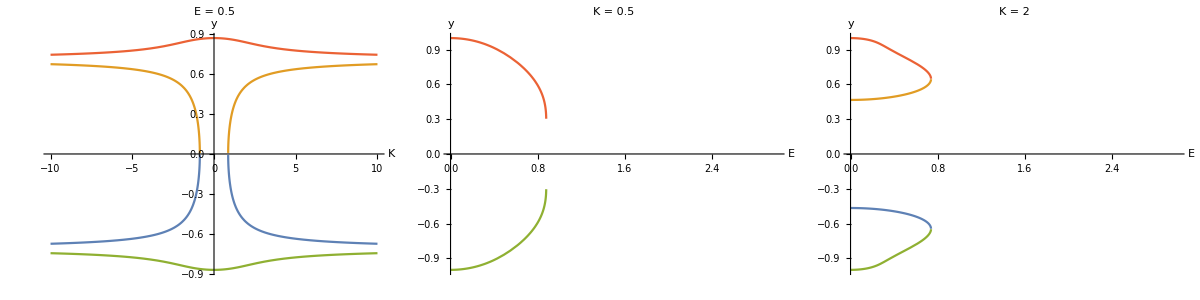

```mathematica
ysolSymmetric=Simplify[Solve[temp5==0,y],Assumptions->{e>0}];
p1=Plot[y/.ysolSymmetric/.e->0.5//Evaluate,{k,-10,10},AxesLabel->{"K","y"},LabelStyle->15,ImageSize->Medium,PlotLabel->"E = 0.5"];
p2=Plot[y/.ysolSymmetric/.k->0.5//Evaluate,{e,0,3},AxesLabel->{"E","y"},LabelStyle->15,ImageSize->Medium,PlotLabel->"K = 0.5"];
p3=Plot[y/.ysolSymmetric/.k->2//Evaluate,{e,0,3},AxesLabel->{"E","y"},LabelStyle->15,ImageSize->Medium, PlotLabel->"K = 2"];
Grid[{{p1,p2,p3}}]
```

Ok, I can see the bifurcation structure here. I think I may be able to infer

## Attempt 3 -- think I solved them exact

### ODEs

```mathematica
Clear[b,j,k]
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Trig --> polynomial

Here I’m only including one branch of fixed points. So I’m searching for *a* fixed point -- not *all* fixed points.

```mathematica
sub={
Cos[xp]->x,
Sin[xp]->p √(1-x^2),
Cos[xm]->y,
Sin[xm]->p √(1-y^2),
Cos[θp]->w,
Sin[θp]->p √(1-w^2),
Cos[θm]->z,
Sin[θm]->p √(1-z^2)
};

TableForm[es]
es1=TrigExpand[es]/.sub;
TableForm[es1]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

e-p x √(1-y^2)
-p √(1-x^2) y-k p y √(1-y^2) z^2+k p^3 y √(1-y^2) (1-z^2)
e-p w √(1-z^2)
-p √(1-w^2) z-k p y^2 z √(1-z^2)+k p^3 (1-y^2) z √(1-z^2)

Looking at these, I can do the elimination x and w easily. I’ll do that first

### Eliminate first two

```mathematica
xwsol=Solve[es1[[{1,3}]]==0,{x,w}]
```

{{x→e/(p √(1-y^2)),w→e/(p √(1-z^2))}}

```mathematica
es2=(es1[[{2,4}]]/.xwsol//Simplify)[[1]]
```

{p y (-√(1+e^2/(p^2 (-1+y^2)))-k √(1-y^2) (z^2+p^2 (-1+z^2))),p z (-k (y^2+p^2 (-1+y^2)) √(1-z^2)-√(1+e^2/(p^2 (-1+z^2))))}

Get rid of the p=± 1

```mathematica
es3=Expand[es2^2/.{p^2->1,p^2->1}]/.p->1//Together//Numerator;
es3//TableForm
```

-y^2+e^2 y^2-k^2 y^2+y^4+2 k^2 y^4-k^2 y^6+2 k y^2 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2))-2 k y^4 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2))+4 k^2 y^2 z^2-8 k^2 y^4 z^2+4 k^2 y^6 z^2-4 k y^2 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2)) z^2+4 k y^4 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2)) z^2-4 k^2 y^2 z^4+8 k^2 y^4 z^4-4 k^2 y^6 z^4
-z^2+e^2 z^2-k^2 z^2+4 k^2 y^2 z^2-4 k^2 y^4 z^2+z^4+2 k^2 z^4-8 k^2 y^2 z^4+8 k^2 y^4 z^4-k^2 z^6+4 k^2 y^2 z^6-4 k^2 y^4 z^6+2 k z^2 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))-4 k y^2 z^2 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))-2 k z^4 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))+4 k y^2 z^4 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))

```mathematica
e2=es3[[1]]/.√(1-y^2) √((-1+e^2+y^2)/(-1+y^2))->X
```

-y^2+e^2 y^2-k^2 y^2+2 k X y^2+y^4+2 k^2 y^4-2 k X y^4-k^2 y^6+4 k^2 y^2 z^2-4 k X y^2 z^2-8 k^2 y^4 z^2+4 k X y^4 z^2+4 k^2 y^6 z^2-4 k^2 y^2 z^4+8 k^2 y^4 z^4-4 k^2 y^6 z^4

```mathematica
Solve[e2==0,X]
```

{{X→(1-e^2+k^2-y^2-2 k^2 y^2+k^2 y^4-4 k^2 z^2+8 k^2 y^2 z^2-4 k^2 y^4 z^2+4 k^2 z^4-8 k^2 y^2 z^4+4 k^2 y^4 z^4)/(2 k (-1+y^2) (-1+2 z^2))}}

```mathematica
e3=Simplify[Numerator[Together[((1-e^2+k^2-y^2-2 k^2 y^2+k^2 y^4-4 k^2 z^2+8 k^2 y^2 z^2-4 k^2 y^4 z^2+4 k^2 z^4-8 k^2 y^2 z^4+4 k^2 y^4 z^4)/(2 k (-1+y^2) (-1+2 z^2)))^2-(√(1-y^2) √((-1+e^2+y^2)/(-1+y^2)))^2]]]
```

(e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2))^2

```mathematica
e4=e3/.{y->z,z->y}
```

(e^2+(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2)))^2

```mathematica
est={e3,e4}/.{y->√y1,z->√z1}//Simplify
```

{(e^2+(-1+y1) (1+k^2 (-1+y1) (1-2 z1)^2))^2,(e^2+(1+k^2 (1-2 y1)^2 (-1+z1)) (-1+z1))^2}

Can I solve these exactly?

```mathematica
sols=Solve[est==0,{y1,z1}]
```

{{y1→-(2-3 k^2)/(4 k^2)+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/k^4+1/k^2-(4 e^2)/k^2+(16 e^2)/(k^3 √(-16 e^2+k^2))-1/(k √(-16 e^2+k^2))),z1→(-16-64 e^2+80 e^4+40 k^2+148+16 k^8 (1)^7+64 e^2 k^8 (-(2-3 k^2)/(4 k^2)+1/1-1/2 √(1/k^4+1/k^2-1/k^2+1-1/(k 1)))^7-1024 e^4 k^8 (-(2-3 k^2)/(4 k^2)+(√(1+k^2))/(4 k)-1/2 √(1/k^4+1/k^2-(4 e^2)/k^2+(16 e^2)/(k^3 √1)-1/(k √(1+k^2))))^7)/(-16 e^4 k^2+20 e^4 k^4-64 e^6 k^4-4 e^4 k^6+16 e^6 k^6)},{y1→-(2-1)/(4 k^2)+1+1/2 √1,z1→1},5,{y1→3/4+1/2 √(1/12+(-12+48 e^2+k^2)/(12 (1)^(1/3))+(5+1)^(1/3)/(12 k^2))+1/2 √(1/6-(-12+48 e^2+k^2)/(12 (5+6 √3 √1)^(1/3))-(5+1)^(1/3)/(12 k^2)+(-12-(2 (1-6 k^2))/k^2)/(4 √(1/12+(-12+48 e^2+k^2)/(12 (1)^(1/3))+(1)^(1/3)/(12 k^2)))),z1→1/(-16 e^4 k^2+5+16 e^6 k^6)}}
 |  |  |  |

Sweet

```mathematica
Length[sols]
```

8

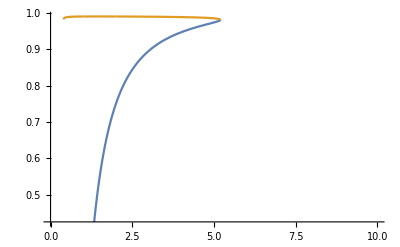
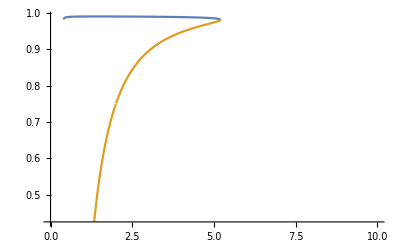
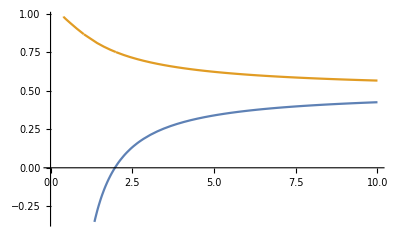
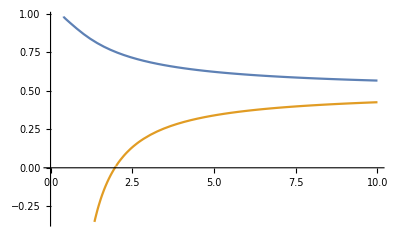
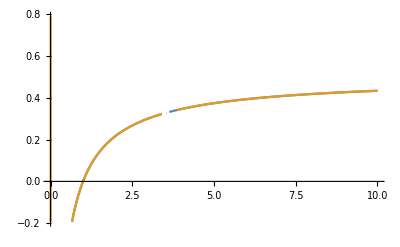
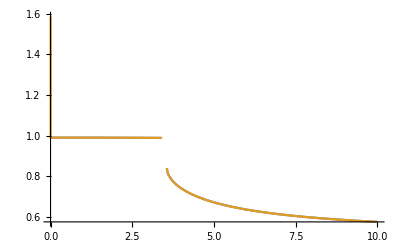
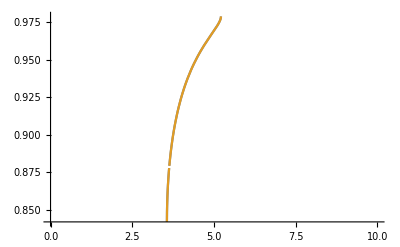
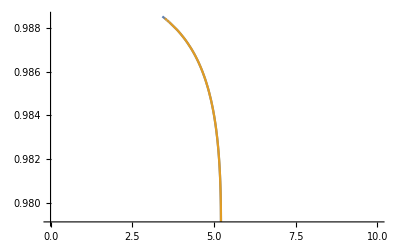

```mathematica
ParallelTable[
Plot[{y1,z1}/.sols[[i]]/.e->0.1//Evaluate,{k,0,10}],
{i,1,Length[sols]}
]
```

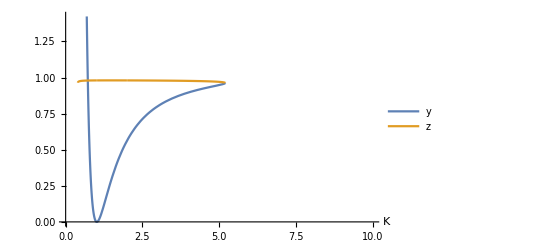
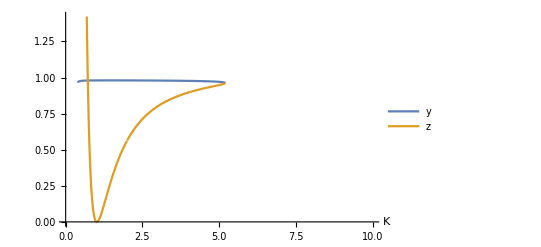
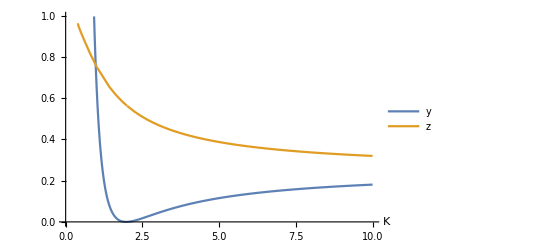
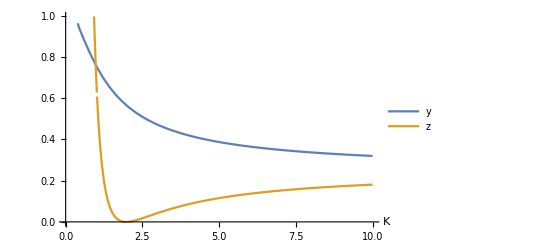
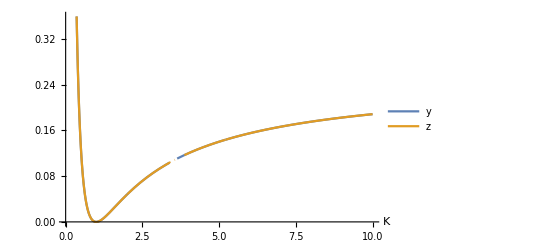
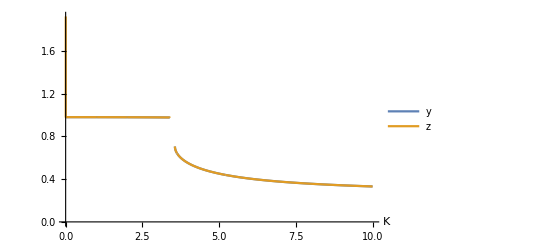
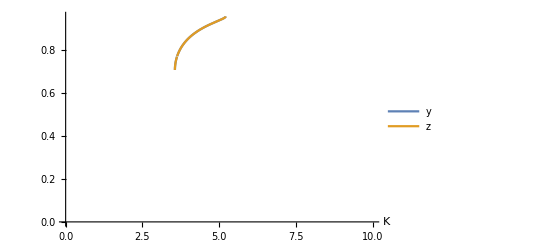
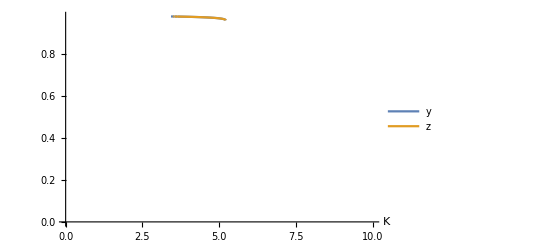

```mathematica
ParallelTable[
Plot[{y1^2,z1^2}/.sols[[i]]/.e->0.1//Evaluate,{k,0,10},AxesOrigin->{0,0},AxesLabel->{"K"},PlotLegends->{"y","z"},LabelStyle->15],
{i,1,Length[sols]}
]
```

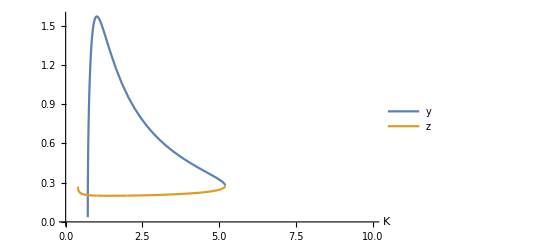
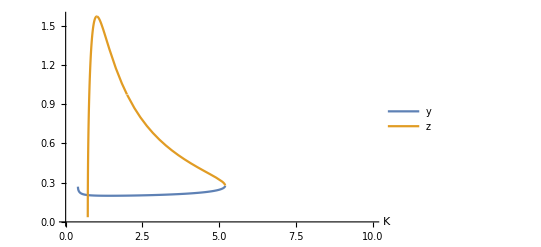
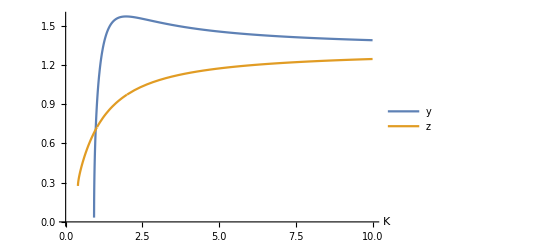
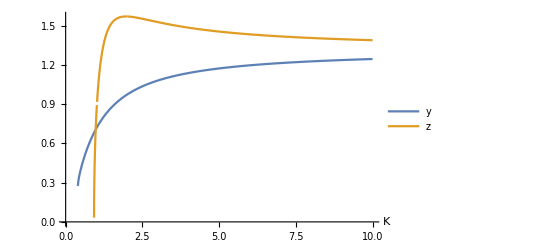
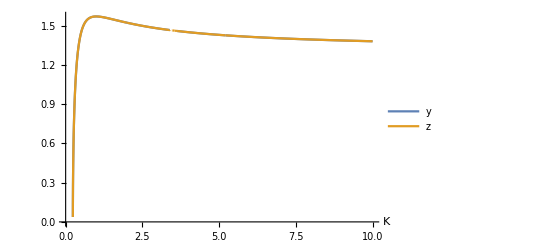
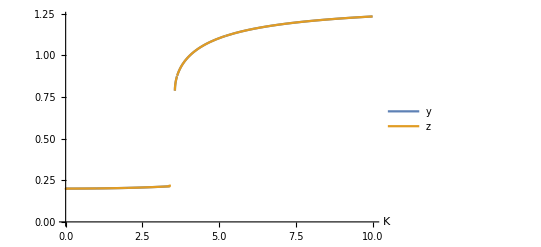
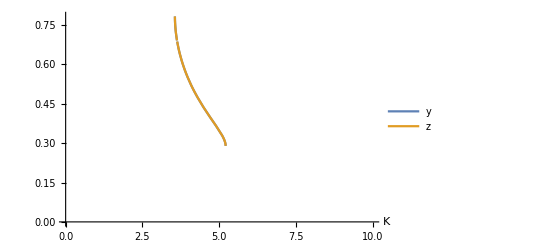
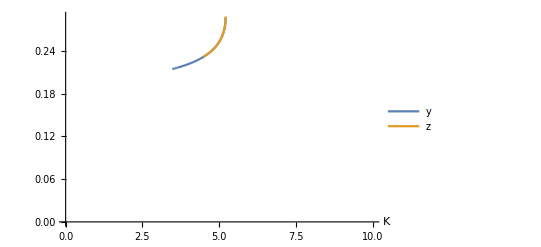

```mathematica
ParallelTable[
Plot[{ArcCos[y1^2],ArcCos[z1^2]}/.sols[[i]]/.e->0.1//Evaluate,{k,0,10},AxesOrigin->{0,0},AxesLabel->{"K"},PlotLegends->{"y","z"},LabelStyle->15],
{i,1,Length[sols]}
]
```

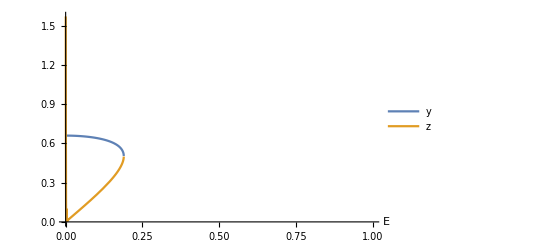
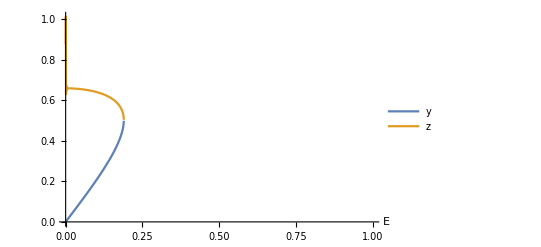
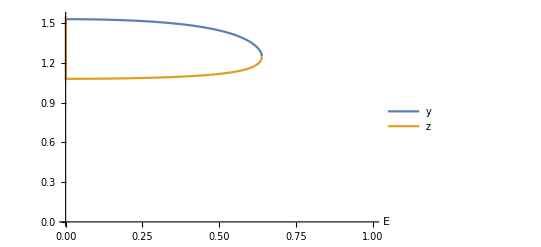
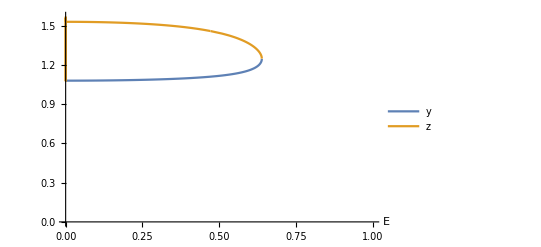
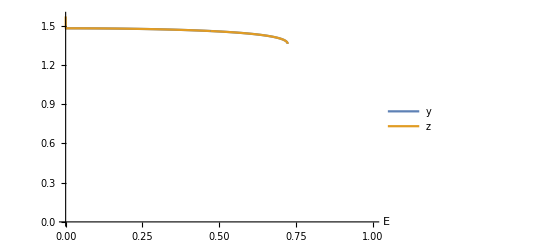
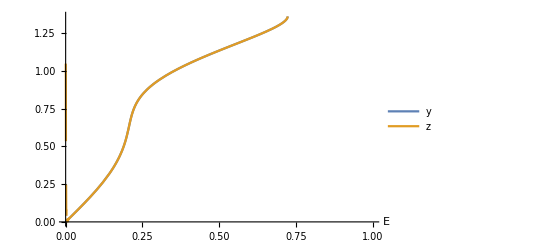
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[
Plot[{ArcCos[y1^2],ArcCos[z1^2]}/.sols[[i]]/.k->3//Evaluate,{e,0,1},AxesOrigin->{0,0},AxesLabel->{"E"},PlotLegends->{"y","z"},LabelStyle->15],
{i,1,Length[sols]}
]
```

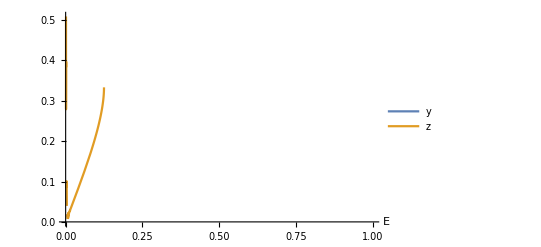
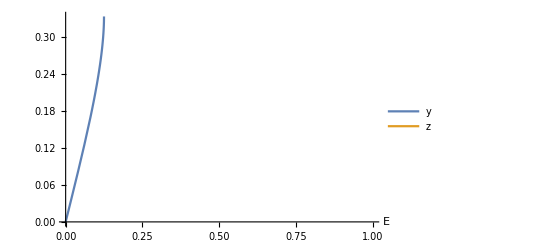
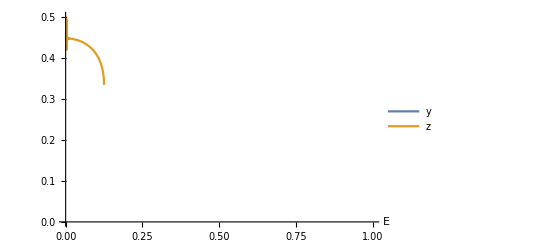
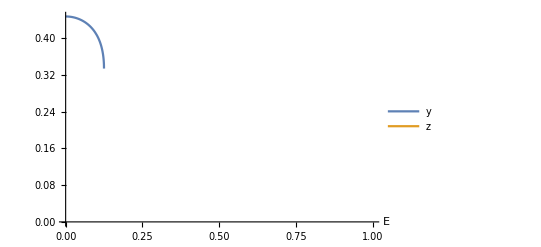
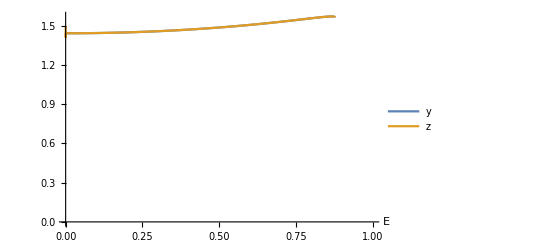
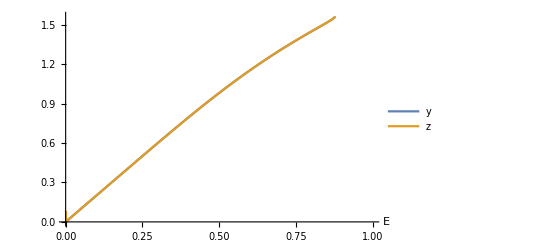
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[
Plot[{ArcCos[y1^2],ArcCos[z1^2]}/.sols[[i]]/.k->0.5//Evaluate,{e,0,1},AxesOrigin->{0,0},AxesLabel->{"E"},PlotLegends->{"y","z"},LabelStyle->15],
{i,1,Length[sols]}
]
```

```mathematica
Simplify[y1/.sols[[1]]]
```

(-2+k √(-16 e^2+k^2)-k^2 (-3+2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4)))/(4 k^2)

```mathematica
Solve[-16 e^2+k^2==0,e]
```

{{e→-k/4},{e→k/4}}

Good. There are the bif points.

### Find expressions for S_±

## Roughwork

```mathematica
y+2x==0
```

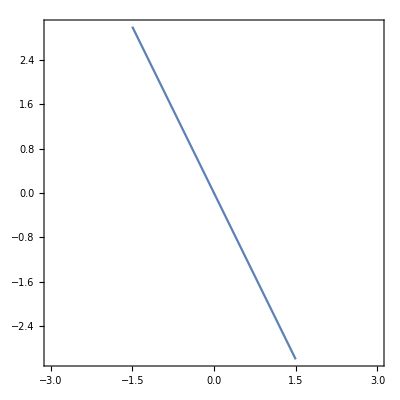

```mathematica
r=y+2x;
ContourPlot[{r==0,r^2==0},{x,-3,3},{y,-3,3}]
```

```mathematica
r^2//Expand
```

4 x^2+4 x y+y^2